# 2 DEG Magneto - electric Properties

## Inverse scattering time matrix diagonal elements ( l=0)

#### Gauss-Hermite Function χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

#### Landau Level N = 0

```mathematica
Q0:= χ[2.342*y2,0]*χ[2.342*(y1-y2),0];
A0[y1_?NumericQ,E_?NumericQ]:=((BesselJ[0,2.090*Sqrt[E]*(y1)])^2)*NIntegrate[Q0^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup0 := NIntegrate[A0[y1,e],{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown0:= NIntegrate[A0[y1,0],{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse0 := Sup0/Sdown0;
```

```mathematica
(*P0=Plot[Sqrt[Tinverse0] ,{e,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{RGBColor["#D98880"]},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];*)
```

#### Landau Level N = 1

```mathematica
Q1:= χ[2.342*y2,1]*χ[2.342*(y1-y2),1];
A1[y1_?NumericQ,E_?NumericQ]:=((BesselJ[0,2.090*Sqrt[E]*(y1)])^2)*NIntegrate[Q1^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup1:= NIntegrate[A1[y1,e],{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown1:= NIntegrate[A0[y1,0],{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse1 := Sup1/Sdown1;
(*P1=Plot[Sqrt[Tinverse1] ,{e,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{RGBColor["#85C1E9"]},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];*)
```

#### Landau Level N = 2

```mathematica
Q2:= χ[2.342*y2,2]*χ[2.342*(y1-y2),2];
A2[y1_?NumericQ,E_?NumericQ]:=((BesselJ[0,2.090*Sqrt[E]*(y1)])^2)*NIntegrate[Q2^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup2:= NIntegrate[A2[y1,e],{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown2:= NIntegrate[A0[y1,0],{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse2 := Sup2/Sdown2;
(*P2=Plot[Sqrt[Tinverse2] ,{e,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{RGBColor["#82E0AA"]},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];*)
```

#### Landau Level N = 3

```mathematica
Q3:= χ[2.342*y2,3]*χ[2.342*(y1-y2),3];
A3[y1_?NumericQ,E_?NumericQ]:=((BesselJ[0,2.090*Sqrt[E]*(y1)])^2)*NIntegrate[Q3^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup3:= NIntegrate[A3[y1,e],{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown3:= NIntegrate[A0[y1,0],{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse3:= Sup3/Sdown3;
(*P3=Plot[Sqrt[Tinverse3] ,{e,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{RGBColor["#BB8FCE"]},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];*)
```

#### Landau Level N = 4

```mathematica
Q4:= χ[2.342*y2,4]*χ[2.342*(y1-y2),4];
A4[y1_?NumericQ,E_?NumericQ]:=((BesselJ[0,2.090*Sqrt[E]*(y1)])^2)*NIntegrate[Q4^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup4:= NIntegrate[A4[y1,e],{y1,-Infinity,Infinity},AccuracyGoal->4];
Sdown4:= NIntegrate[A0[y1,0],{y1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse4:= Sup4/Sdown4;
(*P4=Plot[Sqrt[Tinverse4] ,{e,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{RGBColor["#BB8FCE"]},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50];*)
```

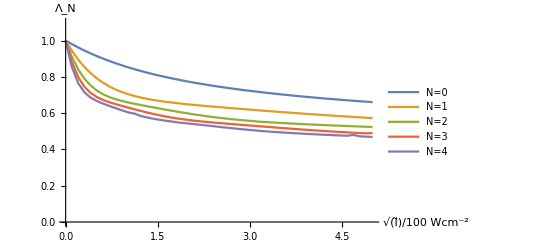

```mathematica
P=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{e,0,5},
PlotRange->{{0,5},{0,1.1}},
PlotLegends->{"N=0","N=1","N=2","N=3","N=4"},AxesLabel->{Style["√OverTilde[<I>]/100 Wcm^-2",FontSize->20,FontColor->Black],Style["Λ_N",FontSize->20,FontColor->Black]},
AxesStyle->{Directive[Black,15],Directive[Black,15]},LabelStyle->Larger,MaxRecursion->0,PlotPoints->50]
```

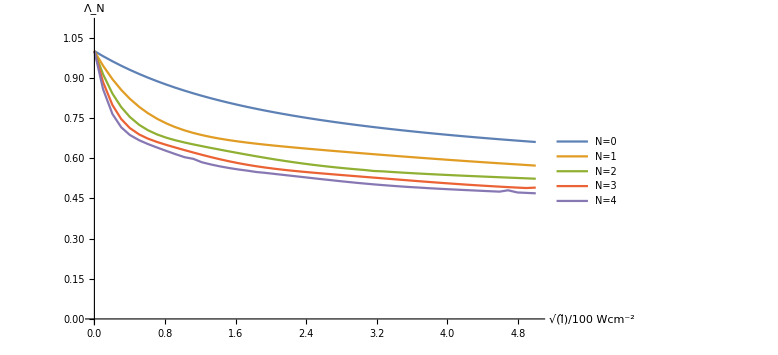

```mathematica
Q=Show[P,ImageSize->Large]
```

#### Special Testing

```mathematica
Q:= χ[y2,5]*χ[(y1+y2),5];
A[y1_?NumericQ]:=NIntegrate[Q^2,{y2,-Infinity,Infinity},AccuracyGoal->4];
Sup = NIntegrate[A[y1],{y1,-Infinity,Infinity},AccuracyGoal->4]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.99981

```mathematica
Export["new2.pdf",Q]
```

new2.pdf